```mathematica
Quit
```

## Parameters of simulation

```mathematica
(*GRAVOTHERMAL SIMULATION*)
beta = 0.6; (*You have to put this by yourself in right place!!!*)
dT = -2.0; (*determination of the next time step, originall: 10^-4 in heat function, put in right place!!!*);
stepsToSave = 10;(*number of recorded steps, you want save. In the gravothermal evolution*);
```

## Take data from csv

```mathematica
inputFile = "./mimimc_M_10.699_t_365.17_sigma_1.0_beta_0.6.txt";
(*Data from all time steps*)
data=Import[NotebookDirectory[]<>inputFile,"Table"];

(*TAKE DATE FROM TXT FILE: LAST TIME STEP*)
lastTime=Last[data][[1]]; (*To get data in the last time step*)
timeTxtLast= Select[data,First[#]==lastTime&][[All,1]];
rTxtLast=Select[data,First[#]==lastTime&][[All,2]];
rhoTxtLast=Select[data,First[#]==lastTime&][[All,3]];
mTxtLast=Select[data,First[#]==lastTime&][[All,5]]; (*in general here should be 4, in gravo 5*)
velDisTxtLast=Select[data,First[#]==lastTime&][[All,4]]; (*in general here should be 5, in gravo 4*)

(*TAKE DATE FROM TXT FILE: MINIMAL DENSITY STEP*)
minDensityTime=SortBy[Select[data,#[[2]]==0.01&],#[[3]]&][[1]][[1]](*YOU HAVE TO MANUALY SET 0.01 or different number*);
timeTxtMinRho =Select[data,First[#]==minDensityTime&][[All,1]];
rTxtMinRho = Select[data,First[#]==minDensityTime&][[All,2]];
rhoTxtMinRho = Select[data,First[#]==minDensityTime&][[All,3]];
mTxtMinRho = Select[data,First[#]==minDensityTime&][[All,4]];
velDisTxtMinRho = Select[data,First[#]==minDensityTime&][[All,5]];

(*VALUES OF PARAMETERS*)
FileParameters = StringSplit[inputFile,"_"];
MassInit = ToExpression[FileParameters[[3]]]; (*initial mass of the halo [10^x Solar Mass]*)
crossSection = ToExpression[FileParameters[[7]]]; (*annihilation cross section[cm^2/g]*)
NumberOfRadi = Length[rTxtLast]; (*number of radi in the range of 10^-2 r_s, 10^2 r_s*)

(*SET THE TIME OF EVOLUTION*)
log10timeBeg = timeTxtLast[[1]];(*timeTxtMinRho[[1]];*) (*log10(time), where [time] = GeV^-1]*)
timeBeg = 10^timeTxtLast[[1]];(*10^timeTxtLast[[1]];*) (*time, where [time] = GeV^-1]*)

timeEnd = 2051.1; (*time, where [time] = GeV^-1]*)
(*timeEnd = 2.5*10^timeTxtLast[[1]]; (*time, where [time] = GeV^-1]*)*)
log10timeEnd =  Log10[timeEnd]; (*log10(time) where [time] = GeV^-1]*)

(*OUTPUT FILES NAMES*)
hydroEquFile = "HydroEqu_M_" <> ToString[MassInit] <> "_sigma_" <> TextString[crossSection] <>  "_beta_" <>TextString[beta]<> ".csv";
(*------------------------------------------------------------------------------------------*)
(*PRINTING TO MAKE SURE*)
Print["rTxt[[1]]: ", rTxtLast[[1]]]
(*Print["velDisTxtLast: ", velDisTxtLast];*)
Print["NumberOfRadi: ",NumberOfRadi]
Print["MassInit: ", MassInit]
Print["crossSection: ", crossSection]
Print["hydroEquFile: ", hydroEquFile]
Print["Ending time of simulation: ", timeEnd, " Gyr"]
Print["Begining time of simulation: ", timeBeg, " Gyr"]
(*Print[rhoTxt]*)
(*Row[{timeBeg, log10timeBeg, timeEnd, log10timeEnd}, ", "]*)
(*Print[rTxt];
Print[rhoTxt];*)
(*ListLogPlot[Table[{rTxt[[j]],velDisTxt[[j]]},{j,1,NR}]];*)
```

Part::partw: Part 5 of {2.5625,0.0404031,2.95295,6.31798} does not exist.

Part::partw: Part 1 of {} does not exist.

rTxt[[1]]: 0.0404031

NumberOfRadi: 400

MassInit: 10.699

crossSection: 1.

hydroEquFile: HydroEqu_M_10.699_sigma_1.0_beta_0.6.csv

Ending time of simulation: 2051.1 Gyr

Begining time of simulation: 365.174 Gyr

## Stuffs

```mathematica
<<MaTeX`
Needs["NumericalCalculus`"]
(*Needs["DifferentialEquations`NDSolveProblems`"];*)
(*Needs["DifferentialEquations`NDSolveUtilities`"];*)
ticks=Flatten[Join[Table[Join[{{10^j,StringForm["10^(``)",j],{0.02,0}}},Table[{i*10^j,""},{i,2,9}]],{j,-200,10}]],1];

ticksNoLabel=Flatten[Join[Table[Join[{{10^j,"",{0.02,0}}},Table[{i*10^j,""},{i,2,9}]],{j,-200,10}]],1];

ticksEven=Flatten[Join[Table[Join[{{10^j,If[Mod[j,2]==0,StringForm["10^(``)",j],""],{0.02,0}}},Table[{i*10^j,""},{i,2,9}]],{j,-200,10}]],1];

ticksOdd=Flatten[Join[Table[Join[{{10^j,If[Mod[j,2]==1,StringForm["10^(``)",j],""],{0.02,0}}},Table[{i*10^j,""},{i,2,9}]],{j,-200,10}]],1];

Logticks=Flatten[Join[Table[Join[{{Log[10,10^j],StringForm["10^(``)",j],{0.02,0}}},Table[{Log[10,i*10^j],""},{i,2,9}]],{j,-30,10}]],1];

LogticksNoLabel=Flatten[Join[Table[Join[{{Log[10,10^j],"",{0.02,0}}},Table[{Log[10,i*10^j],""},{i,2,9}]],{j,-20,10}]],1];

LogticksEven=Flatten[Join[Table[Join[{{Log[10,10^j],If[Mod[j,2]==0,StringForm["10^(``)",j],""],{0.02,0}}},Table[{Log[10,i*10^j],""},{i,2,9}]],{j,-20,10}]],1];

Logticks3=Flatten[Join[Table[Join[{{Log[10,10^j],If[Mod[j,3]==0,StringForm["10^(``)",j],""],{0.02,0}}},Table[{Log[10,i*10^j],""},{i,2,9}]],{j,-20,10}]],1];

GridPointPlot[{u->if_InterpolatingFunction},t_,opts___]:=Module[{grid=InterpolatingFunctionCoordinates[if][[1]]},ListPlot[Transpose[{grid,if[grid,t]}],opts]]
```

## Compile functions (must evaluate this section before evaluating anything.)

```mathematica
hydroeq=Compile[{{ρ,_Real,1},{r,_Real,1},{σ,_Real,1},{M,_Real,1},{tG,_Real},{t0,_Real}},Module[{n=Length@ρ,inv=ρ,ϕ=ρ,ψ=ρ,aϕ=ρ,bϕ=ρ,cϕ=ρ,dϕ=ρ,aψ=ρ,bψ=ρ,cψ=ρ,dψ=ρ,α=ρ,γ=ρ,δr=ρ,δρ=ρ,nρ=ρ,nσ=σ,nr=r, index =ρ},
Do[
index[[1]] = k;(*I ADDED BY KRZYSZTOF*)
Do[inv[[j]]=(nσ[[j]])^3/nρ[[j]],{j,1,n}];
Do[ϕ[[j]]=(nρ[[j]]^(5/3) inv[[j]]^(2/3)-nρ[[j-1]]^(5/3) inv[[j-1]]^(2/3))/(M[[j]]-M[[j-1]])+((t0/tG)^2 (M[[j]]+M[[j-1]]))/(2 π^2 (nr[[j]]+nr[[j-1]])^4),{j,2,n}];
Do[ψ[[j]]=(M[[j]]-M[[j-1]])/(nr[[j]]-nr[[j-1]])-1/2 π (nr[[j]]+nr[[j-1]])^2 (nρ[[j]]+nρ[[j-1]]),{j,2,n}];
(**)
Do[aϕ[[j]]=-((2 (t0/tG)^2 (M[[j]]+M[[j-1]]))/(π^2 (nr[[j]]+nr[[j-1]])^5)),{j,2,n}];
Do[bϕ[[j]]=-((5 (nρ[[j-1]]^(2/3) inv[[j-1]]^(2/3)))/(3 (M[[j]]-M[[j-1]]))),{j,2,n}];
Do[cϕ[[j]]=-((2 (t0/tG)^2 (M[[j]]+M[[j-1]]))/(π^2 (nr[[j]]+nr[[j-1]])^5)),{j,2,n}];
Do[dϕ[[j]]=(5 (nρ[[j]]^(2/3) inv[[j]]^(2/3)))/(3 (M[[j]]-M[[j-1]])),{j,2,n}];
Do[aψ[[j]]=(M[[j]]-M[[j-1]])/(nr[[j]]-nr[[j-1]])^2-π (nr[[j]]+nr[[j-1]]) (nρ[[j]]+nρ[[j-1]]),{j,2,n}];
Do[bψ[[j]]=1/2 (-π) (nr[[j]]+nr[[j-1]])^2,{j,2,n}];
Do[cψ[[j]]=-((M[[j]]-M[[j-1]])/(nr[[j]]-nr[[j-1]])^2)-π (nr[[j]]+nr[[j-1]]) (nρ[[j]]+nρ[[j-1]]),{j,2,n}];
Do[dψ[[j]]=1/2 (-π) (nr[[j]]+nr[[j-1]])^2,{j,2,n}];
(**)
α[[1]]=0;
Do[α[[j]]=(dϕ[[j]] (bψ[[j]]-aψ[[j]] α[[j-1]])-dψ[[j]] (bϕ[[j]]-aϕ[[j]] α[[j-1]]))/(cϕ[[j]] (bψ[[j]]-aψ[[j]] α[[j-1]])-cψ[[j]] (bϕ[[j]]-aϕ[[j]] α[[j-1]])),{j,2,n}];
γ[[1]]=0;
Do[γ[[j]]=((bψ[[j]]-aψ[[j]] α[[j-1]]) (ϕ[[j]]-aϕ[[j]] γ[[j-1]])-(bϕ[[j]]-aϕ[[j]] α[[j-1]]) (ψ[[j]]-aψ[[j]] γ[[j-1]]))/(cϕ[[j]] (bψ[[j]]-aψ[[j]] α[[j-1]])-cψ[[j]] (bϕ[[j]]-aϕ[[j]] α[[j-1]])),{j,2,n}];
(**)
δρ[[n]]=0;
δr[[n]]=-γ[[n]];
Do[δρ[[n-j]]=-((ψ[[n-j+1]]-aψ[[n-j+1]] γ[[n-j]]+cψ[[n-j+1]] δr[[n-j+1]]+dψ[[n-j+1]] δρ[[n-j+1]])/(bψ[[n-j+1]]-aψ[[n-j+1]] α[[n-j]]));
δr[[n-j]]=-γ[[n-j]]-α[[n-j]]*δρ[[n-j]];,{j,1,n-1}];
(**)
If[Max[Table[Abs[δr[[j]]/r[[j]]],{j,1,n}]]<10^-4.(*convergence criterion, originall: 10^-4. DO NOT CHANGE IT!*),Break[]];
Do[nr[[j]]=nr[[j]]+δr[[j]],{j,1,n}];
Do[nρ[[j]]=nρ[[j]]+δρ[[j]],{j,1,n}];
Do[nσ[[j]]=(nρ[[j]]*inv[[j]])^(1/3),{j,1,n}];
,{k,0,10^10}];
(**)
{nr,nρ,nσ, index}
]
,CompilationTarget->"C",RuntimeOptions->"Speed"];
(**)
heat=Compile[{{ρ,_Real,1},{r,_Real,1},{σ,_Real,1},{M,_Real,1},{ξ,_Real,1},{tG,_Real},{t0,_Real},{m,_Real},{r0,_Real},{ρ0,_Real}},
Module[{n=Length@ρ,nρ=ρ,nσ=σ,nr=r,nξ=ξ,κ=r,L=r,δucond=r,δusemi=r,δu=r,δT=r},
Do[κ[[j]]=((nσ[[j]]*(3/2 *(25(π)^(1/2))/32))^-1+(((2.18428*10^-6*m*t0)/(r0*nξ[[j]]*ρ0))/tG)^2*(3/2*0.6*(16/π)^(1/2)* (nρ[[j]]*nσ[[j]]^3))^-1)^-1,{j,1,n}];
L[[1]]=0;
Do[L[[j]]=((2.18428*10^-6*m*t0)/(r0*nξ[[j]]*ρ0)(*tel*))/t0*4 π nr[[j]]^2*κ[[j]]*Piecewise[{{(nσ[[j+1]]^2-nσ[[j-1]]^2)/(nr[[j+1]]-nr[[j-1]]),1<j<n},{(-nσ[[j+2]]^2+4 nσ[[j+1]]^2-3 nσ[[j]]^2)/(nr[[j+2]]-nr[[j]]),j==1},{(3 nσ[[j]]^2-4 nσ[[j-1]]^2+nσ[[j-2]]^2)/(nr[[j]]-nr[[j-2]]),j==n}}],{j,2,n}];
Do[δucond[[j]]=Piecewise[{{(L[[j+1]]-L[[j-1]])/(M[[j+1]]-M[[j-1]]),1<j<n},{(-L[[j+2]]+4 L[[j+1]]-3 L[[j]])/(M[[j+2]]-M[[j]]),j==1},{(3 L[[j]]-4 L[[j-1]]+L[[j-2]])/(M[[j]]-M[[j-2]]),j==n}}],{j,1,n}];
Do[δu[[j]]=(δucond[[j]])/(3/2 nσ[[j]]^2),{j,1,n}];
δT[[1]]=(Max[Table[Abs[δu[[j]]],{j,1,n}]])^-1*10^-2.(*determination of the next time step, originall: 10^-4: change to 10^-3*);
Do[nσ[[j]]=(Sqrt[2/3*((3/2 nσ[[j]]^2)+(δucond[[j]])*δT[[1]])]),{j,1,n}];
{δT,nσ,δu}
]
,CompilationTarget->"C",RuntimeOptions->"Speed"];
(**)
(*concentration-mass relation*)
ρc=1.8791*(h^2)*1.4771*10^-7(*Solar Mass/(pc)^3*);
h=0.671;
a[z_]:=0.520+(0.905-0.520)*Exp[-0.617*z^1.21];
b[z_]:=-0.101+0.026*z;
c[M_,z_]:=10^a[z]*(M/((10^12)*(h^-1)(*Solar Mass*)))^b[z]*(13.3199/13.3199)(*5.26*(M/10^14)^-0.1*);
r0[M_,z_]:=(200*4/3 π*ρc)^(-1/3)*M^(1/3)*(c[M,z])^-1*10^-3(*in kpc*);
ρ0[M_,z_]:=M/(4 π*(r0[M,z]*10^3)^3) (1/(-(c[M,z]/(1+c[M,z]))+Log[1+c[M,z]]))(*ρc/3*c[M,z]^3*(-(c[M,z]/(1+c[M,z]))+Log[1+c[M,z]])^-1*)(*in Solar Mass/pc^3*);
z=0;
Mi=MassInit;(*match the range in "Evolution"*)
Mf=10.9;
NM=1;
δM=(Mf-Mi)/NM;
Do[M200[i]=10^(Mi+δM*i),{i,0,NM}];
Do[RS[i]=r0[M200[i],0],{i,0,NM}]
Do[DS[i]=ρ0[M200[i],0],{i,0,NM}]
Table[M200[i],{i,0,NM}]
Table[RS[i],{i,0,NM}]
Table[DS[i],{i,0,NM}]
Clear[Mi,Mf,NM,r0,ρ0,z,a,b,c,h,ρc,M];
```

{5.00035×10^10,7.94328×10^10}

{6.90436,8.44159}

{0.00759172,0.00676539}

## Evolution

```mathematica
SetDirectory[NotebookDirectory[]];(*output directory*)
(**)
Mi=MassInit;(*to scan halo masses, change also "p" range below*)(*match the range in "Compile functions"*)
Mf=10.9;
NM=1;
δM=(Mf-Mi)/NM;
myIndexList = {};
kList =CreateDataStructure["DynamicArray"];
deltaTList = CreateDataStructure["DynamicArray"];
deltaUsol = CreateDataStructure["DynamicArray"];
rarraysol = CreateDataStructure["DynamicArray"];
(**)
AbsoluteTiming[Do[(*mass loop*)
Print["M="<>ToString[Mi+δM*p]];
(*Set up initial r-grid in Log-bin*)
ri=-2.(*Log10[Subscript[r, i=1]/Subscript[r, 0]]*);(*-4 for rSIDM*)
rf=2.(*Log10[Subscript[r, i=NR]/Subscript[r, 0]]*);(*2 for rSIDM*)
NR=NumberOfRadi;(*700 for rSIDM*)
δR=(rf-ri)/NR;
(*NFW scale parameters for given halo mass*)
rs=RS[p](*in kpc*);
ρs=DS[p](*in Solarmass/pc^3*);
(**)
G=1/((1.220890 10^19)^2)(*GeV^-2*);
m=1(*GeV*)(*dummy variable: do not change this!*);
r0=rs*1.56 10^35(*in GeV^-1,1 kpc*);
t0=4.79 10^40(*in GeV^-1*)(*1 Gyr*);
ρ0=(ρs)*2.94*10^-40(*Gev^4,Solarmass/pc^3*);(*Subscript[σ, 0] = Subscript[r, 0]/Subscript[t, 0]*)
tG=√(1/(4 π G ρ0));
(**)
t=timeBeg;
Tticker=0;
ticker=1;
(*set r-grid*)
r[0]=0;
Do[r[j+1]=rTxtLast[[j+1]],{j,0,NR-1}];
(*initial ρ-grid*)
ρ[0]=rhoTxtLast[[1]];(*rhoTxtLast[[1]]; 2.4786890076497015;*)
Do[ρ[j+1]=rhoTxtLast[[j+1]],{j,0,NR-1}];
(*initial M-grid*)
M[0]=0;
(*Do[M[j+1]=mTxtLast[[j+1]],{j,0,NR-1}];*)
M[1]=4/3π * r[1]^3*ρ[1];
Do[M[j]=M[j-1]+(π/2)*(r[j]+r[j-1])^2*(ρ[j]+ρ[j-1])*(r[j]-r[j-1]),{j,2,NR}];
(*initial σ-grid*)
σ[0] = velDisTxtLast[[1]];(*velDisTxtLast[[1]]; 6.161387998905594;*)
Do[σ[j+1]=velDisTxtLast[[j+1]],{j,0,NR-1}];
(**)
ρarray=Table[ρ[j],{j,0,NR}];
(*Print["ρarray: ", ρarray];
Print["Length[ρarray]: ", Length[ρarray]];*)
rarray=Table[r[j],{j,0,NR}];
(*Print["rarray: ", rarray];
Print["Length[rarray]: ", Length[rarray]];*)
σharray=Table[σ[j],{j,0,NR}](*not σarray!*);
(*Print["σharray: ", σharray];
Print["Length[σharray]: ", Length[σharray]];*)
Marray=Table[M[j],{j,0,NR}];
(*Print["Marray: ", Marray];
Print["Length[Marray]: ", Length[Marray]];*)
Clear[ρ,r,σ];
(*hydrodynamic equlibrium*)
neweq=hydroeq[ρarray,rarray,σharray,Marray,tG,t0];
rarray=neweq[[1]];
ρarray=neweq[[2]];
σarray=neweq[[3]];
(*Export data after hydrodynamic equlibrium*)
(*Export[hydroEquFile,Transpose[{rarray,ρarray,σarray}],"TSV"];*)
Do[(*time loop*)
(*Update SIDM cross section distribution with respect to the new equilibrium profile*)
ξarray=Table[(*ξ=*)(crossSection(*10^σmRSIDMint[Log10[σarray[[j]]*r0/t0]]*))/(1(*cm^2/g*))*0.01,{j,1,NR+1}];(*velocity dependence taken into account*)
(*Heat velocity dispersion.*)
h=heat[ρarray,rarray,σarray,Marray,ξarray,tG,(*tJ,*)t0,m,r0,ρ0];
δT=h[[1]][[1]](*time evolution step*);
σharray=h[[2]](*heated velocity dispersion*);
deltaU = h[[3]];
t=t+δT;
(*Find new hydrostatic equilibrium.*)
neweq=hydroeq[ρarray,rarray,σharray,Marray,tG,t0];
rarray=neweq[[1]];
ρarray=neweq[[2]];
σarray=neweq[[3]];
kindex = neweq[[4]][[1]];(*Added index k*)
(*Add values to list*)
kList["Append", kindex];
deltaTList["Append",δT ];
deltaUsol["Append", deltaU];
rarraysol["Append",rarray ];
(*Record solution for the specified time slice, and print Kn*)
If[
Log10[t]≥log10timeBeg(*initial time when you wish to start recording, Log10[Subscript[t, i]/t0]*)+0.0025(*time resolution that you wish to record*)*Tticker∧ticker==1,
Do[ρsol[Tticker][j]=ρarray[[j+1]],{j,0,NR}];
Do[rsol[Tticker][j]=rarray[[j+1]],{j,0,NR}];
Do[σsol[Tticker][j]=σarray[[j+1]],{j,0,NR}];
T[Tticker]=Log10[t];
Kn=√(4 π G ρarray[[1]]*ρ0)*1/(ρarray[[1]]*(ξarray[[1]]/0.01*4578.17)*σarray[[1]])*1/((r0 ρ0)/t0);
myIndexList=AppendTo[myIndexList,i];
Print["-------------------------------------------------------------------"];
Print["numerical step, i: ", i, " ,steps in between: ", Last[myIndexList]-myIndexList[[-2]]];
Print["heat time step, δT: ", δT, " , average δT: ", Mean[deltaTList["Elements"]]];
Print["hydrodynamic index k: ", kindex, " , average k: ", Mean[kList["Elements"]]];
Print["Solved for log10(t)="<>ToString[T[Tticker]]<>", Kn="<>ToString[Kn]];
(**)
kList = CreateDataStructure["DynamicArray"];
(*deltaTList = CreateDataStructure["DynamicArray"];*)
Tticker=Tticker+1;
ticker=0;
ticker=1;
];
If[Tticker > stepsToSave,(*condition to finish computation*)
Do[ρsol[Tticker][j]=ρarray[[j+1]],{j,0,NR}];
Do[rsol[Ttiscker][j]=rarray[[j+1]],{j,0,NR}];
Do[σsol[Tticker][j]=σarray[[j+1]],{j,0,NR}];
T[Tticker]=Log10[t];
T[Tticker]=Log10[t];
Kn=√(4 π G ρarray⟦1⟧ ρ0)*1/(ρarray⟦1⟧*(ξarray[[1]]/0.01*4578.17)* σarray⟦1⟧)*1/((r0 ρ0)/t0);
Print["Solved for t="<>ToString[T[Tticker]]<>", Kn="<>ToString[Kn]];
Break[];
timeEnd = 10^(T[Tticker])
];
If[(*ρarray[[1]]>101.*)Log10[t]>Log10[timeEnd],(*condition to finish computation*)
Do[ρsol[Tticker][j]=ρarray[[j+1]],{j,0,NR}];
Do[rsol[Ttiscker][j]=rarray[[j+1]],{j,0,NR}];
Do[σsol[Tticker][j]=σarray[[j+1]],{j,0,NR}];
T[Tticker]=Log10[t];
Kn=√(4 π G ρarray⟦1⟧ ρ0)*1/(ρarray⟦1⟧*(ξarray[[1]]/0.01*4578.17)* σarray⟦1⟧)*1/((r0 ρ0)/t0);
Print["Solved for t="<>ToString[T[Tticker]]<>", Kn="<>ToString[Kn]];
Break[];
];
Clear[δT];
,{i,0,10^10}];
Print["Exporting data..."];
datasolfinal=Flatten[Table[{T[i],rsol[i][j],ρsol[i][j], σsol[i][j]},{i,0,Tticker},{j,0,NR}],1];
Export["gravoTest_M_" <> ToString[MassInit] <> "_t_" <> 
    TextString[timeEnd] <> "_sigma_" <> TextString[crossSection] <>  "_beta_" <>TextString[beta]<>"_dT_"<>TextString[dT]<>
    ".csv", datasolfinal, "Table"];
Print["Data export complete!"];
,{p,0,0}];](*change it to {p,0,NM}, to scan halo masses*)
Print["Job ended."]
```

M=10.699

-------------------------------------------------------------------

Part::partw: Part -2 of {0} does not exist.

numerical step, i: 0 ,steps in between: -{0}⟦-2⟧

heat time step, δT: 0.00318482 , average δT: 0.00318482

hydrodynamic index k: 1. , average k: 1.

Solved for log10(t)=2.5625, Kn=171.358

-------------------------------------------------------------------

numerical step, i: 6513 ,steps in between: 6513

heat time step, δT: 0.00358635 , average δT: 0.000324081

hydrodynamic index k: 0. , average k: 0.00445263

Solved for log10(t)=2.565, Kn=171.055

-------------------------------------------------------------------

numerical step, i: 14629 ,steps in between: 8116

heat time step, δT: 0.000299351 , average δT: 0.000289033

hydrodynamic index k: 0. , average k: 0.00160177

Solved for log10(t)=2.5675, Kn=170.792

-------------------------------------------------------------------

numerical step, i: 21464 ,steps in between: 6835

heat time step, δT: 0.000044159 , average δT: 0.000296348

hydrodynamic index k: 0. , average k: 0.00190198

Solved for log10(t)=2.57, Kn=170.525

-------------------------------------------------------------------

numerical step, i: 26369 ,steps in between: 4905

heat time step, δT: 1.18126 , average δT: 0.000346895

hydrodynamic index k: 1. , average k: 0.00203874

Solved for log10(t)=2.57325, Kn=170.153

-------------------------------------------------------------------

numerical step, i: 32362 ,steps in between: 5993

heat time step, δT: 0.00865844 , average δT: 0.000329654

hydrodynamic index k: 0. , average k: 0.00166861

Solved for log10(t)=2.57501, Kn=169.933

-------------------------------------------------------------------

numerical step, i: 38168 ,steps in between: 5806

heat time step, δT: 0.016533 , average δT: 0.000336541

hydrodynamic index k: 0. , average k: 0.00155012

Solved for log10(t)=2.57751, Kn=169.697

-------------------------------------------------------------------

numerical step, i: 43644 ,steps in between: 5476

heat time step, δT: 1.07044 , average δT: 0.000366499

hydrodynamic index k: 1. , average k: 0.00219138

Solved for log10(t)=2.58112, Kn=169.256

-------------------------------------------------------------------

numerical step, i: 47128 ,steps in between: 3484

heat time step, δT: 2.46016 , average δT: 0.000414443

hydrodynamic index k: 1. , average k: 0.00200918

Solved for log10(t)=2.58513, Kn=168.787

-------------------------------------------------------------------

numerical step, i: 47129 ,steps in between: 1

heat time step, δT: 0.000123542 , average δT: 0.000414436

hydrodynamic index k: 0. , average k: 0.

Solved for log10(t)=2.58513, Kn=168.799

-------------------------------------------------------------------

numerical step, i: 54719 ,steps in between: 7590

heat time step, δT: 0.412677 , average δT: 0.000396636

hydrodynamic index k: 1. , average k: 0.00158103

Solved for log10(t)=2.58757, Kn=168.501

Solved for t=2.58757, Kn=168.501

Exporting data...

Data export complete!

{13.7829,Null}

Job ended.

```mathematica
ρsol[Tticker-1][0]
```

3.82171

```mathematica
NotebookDirectory[]
```

/Users/ayuki/Downloads/

```mathematica
dataρsolfinal=Flatten[Table[{T[i],rsol[i][j],ρsol[i][j]},{i,0,Tticker-1},{j,0,NR+1}],1];
(*Export["ρsol_M_"<>ToString[10.9]<>"_σ0_0.001.txt",dataρsolfinal,"Table"];*)
dataσsolfinal=Flatten[Table[{T[i],rsol[i][j],σsol[i][j]},{i,0,Tticker-1},{j,0,NR+1}],1];
(*Export["σsol_M_"<>ToString[10.9]<>"_σ0_0.001.txt",dataσsolfinal,"Table"];*)
Print["Data export complete!"];
```

Data export complete!

```mathematica
ρint=Interpolation[dataρsolfinal,InterpolationOrder->1]
```

InterpolatingFunction[{{-3.99811, 1.145}, {0., 100.005}}, <>]

```mathematica
Plot3D[Log10[ρint[t,10^r]],{t,-4,1.15},{r,-2,2},PlotPoints->100]
```

-Graphics3D-

## deltaT

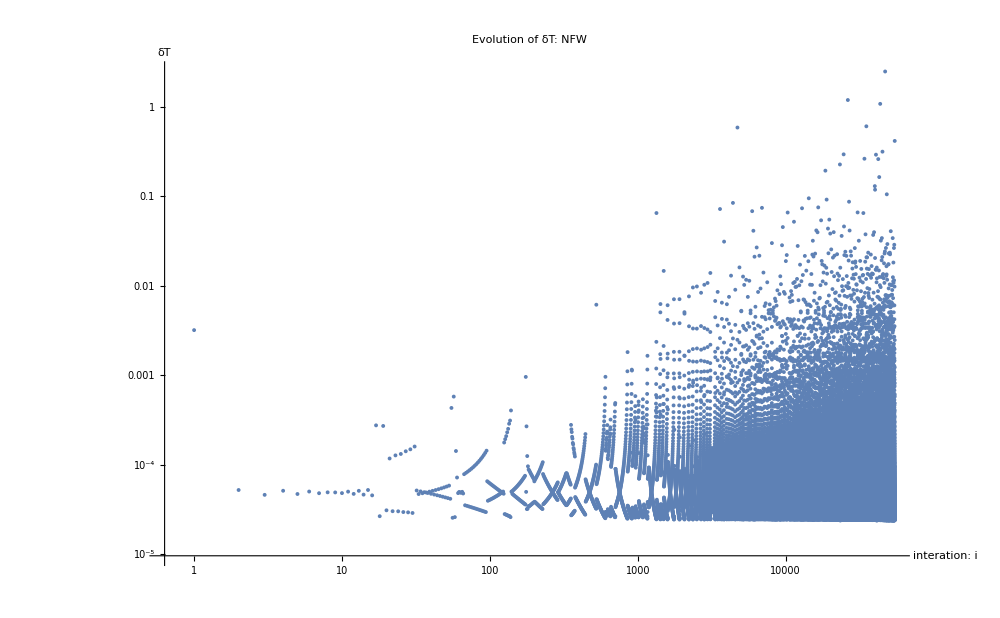

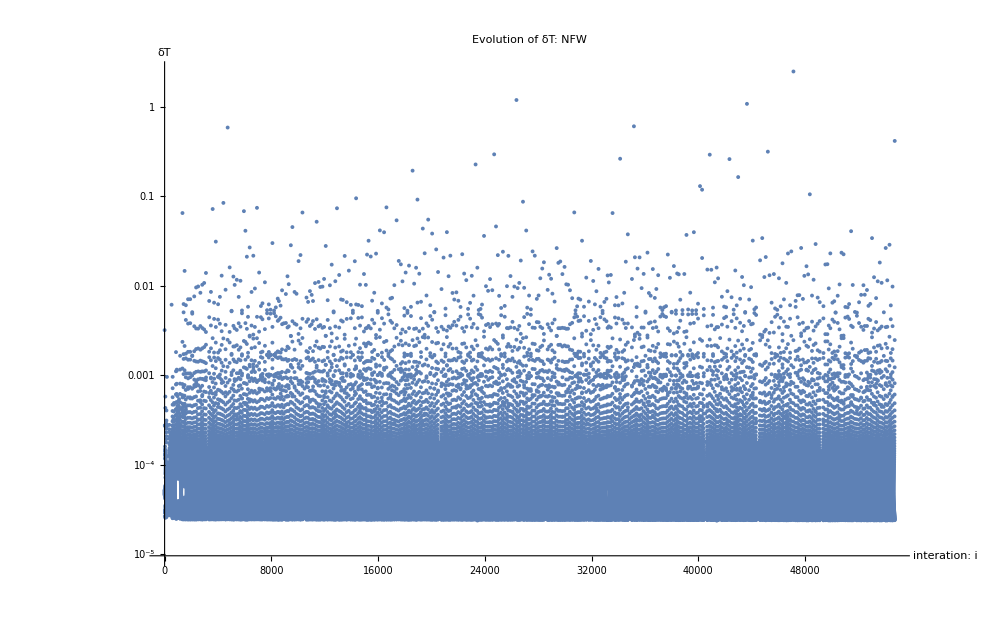

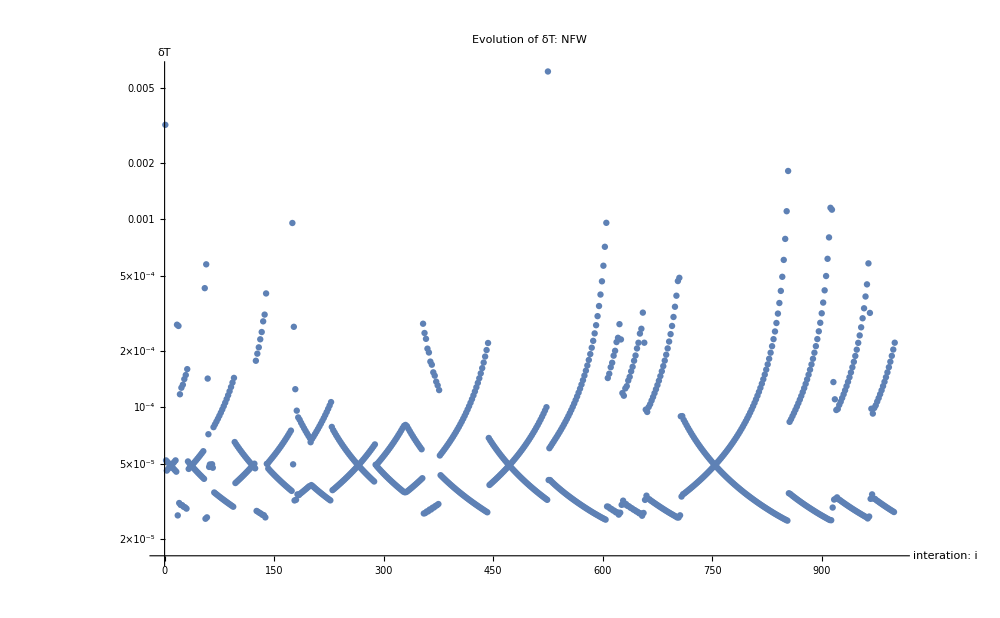

evolution-dT-1.pdf

evolution-dT-2.pdf

evolution-dT-3.pdf

```mathematica
(*FIRST PLOT: Here we will have evolution of the deltaT*)
deltaTListAsList=deltaTList["Elements"];
plot1 =ListLogLogPlot[deltaTListAsList,AxesLabel->{"interation: i","δT"},
ImageSize->{1000,800}  (*Custom size:1200 pixels wide,800 pixels tall*),
PlotLabel->"Evolution of δT: NFW"]
(*SECOND PLOT*)
plot2 = ListLogPlot[deltaTListAsList,AxesLabel->{"interation: i","δT"},
ImageSize->{1000,800}  (*Custom size:1200 pixels wide,800 pixels tall*),
PlotLabel->"Evolution of δT: NFW"]
(*THIRD PLOT*)
sublist=Take[deltaTListAsList,1000];
plot3 = ListLogPlot[sublist,AxesLabel->{"interation: i","δT"},
ImageSize->{1000,800}  (*Custom size:1200 pixels wide,800 pixels tall*),
PlotLabel->"Evolution of δT: NFW"]
(*Export the plot as PDF*)
Export["evolution-dT-1.pdf",plot1]
(*Export the plot as PDF*)
Export["evolution-dT-2.pdf",plot2]
(*Export the plot as PDF*)
Export["evolution-dT-3.pdf",plot3]
```

## DeltaU

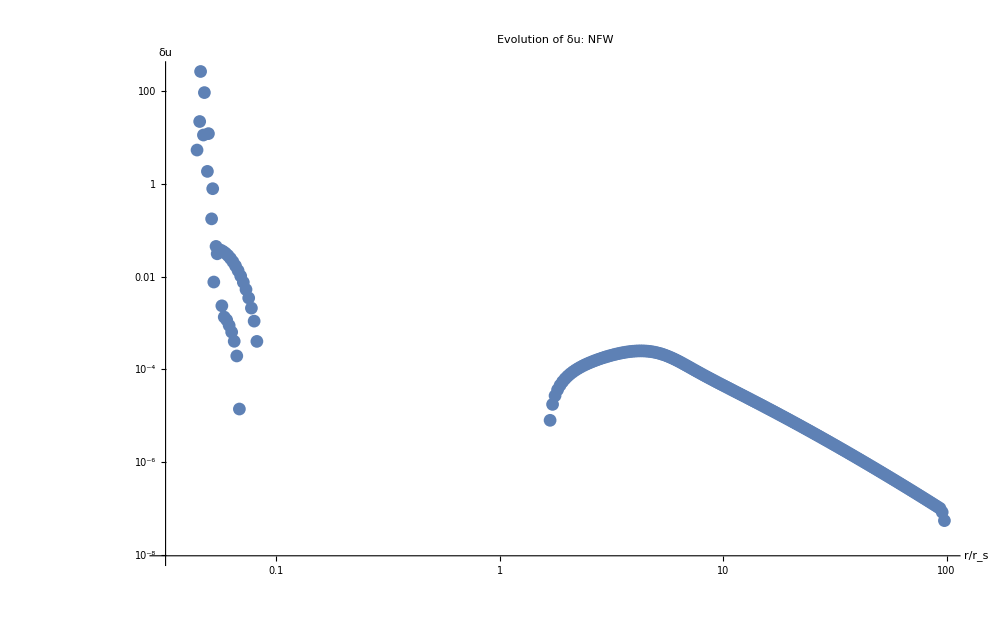

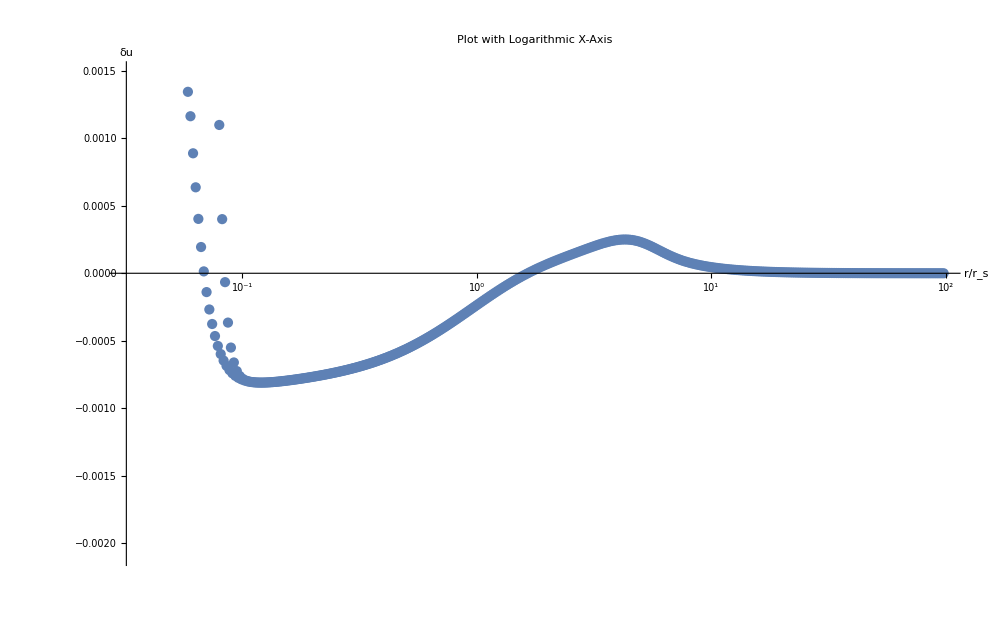

evolution1-du-iteration-170.pdf

evolution2-du-iteration-170.pdf

{-0.00137903,-0.000245298,-0.0000623398,-0.0221523,-0.00225626,0.024232,0.000365697,-0.0181566,-0.00152482,0.00807416,-0.000449939,-0.00437333,-0.000983865,0.000433283,-0.000790038,-0.00114517,-0.000745843,-0.000759257,-0.000887316,-0.000757041,-0.000764647,-0.000876131,-0.000813116,-0.00077467,-0.000814803,-0.000834599,-0.000792529,-0.000816241,-0.000809505,-0.000815661,-0.000799429,-0.000818963,-0.000802901,-0.000813096,-0.000802057,-0.000812144,-0.000802421,-0.000808593,-0.000803058,-0.000805977,-0.000803398,-0.000803521,-0.000803987,-0.000801607,-0.00080421,-0.000800339,-0.000804379,-0.000799647,-0.000804251,-0.0007995,-0.000803939,-0.00079972,-0.000803435,-0.000800173,-0.000802796,-0.00080068,-0.000802078,-0.000801121,-0.000801326,-0.000801392,-0.00080058,-0.000801443,-0.00079986,-0.000801254,-0.000799175,-0.000800839,-0.000798519,-0.000800228,-0.000797878,-0.000799462,-0.000797232,-0.00079858,-0.00079656,-0.000797615,-0.000795843,-0.000796592,-0.000795066,-0.000795526,-0.000794218,-0.000794422,-0.000793293,-0.000793279,-0.000792286,-0.000792094,-0.000791196,-0.000790859,-0.000790023,-0.000789568,-0.000788768,-0.000788214,-0.00078743,-0.00078679,-0.000786007,-0.00078529,-0.000784496,-0.00078371,-0.000782894,-0.000782041,-0.000781194,-0.000780278,-0.000779392,-0.000778412,-0.000777481,-0.000776435,-0.000775455,-0.000774339,-0.000773307,-0.000772117,-0.000771029,-0.000769759,-0.000768616,-0.000767259,-0.000766058,-0.000764608,-0.000763348,-0.000761799,-0.000760477,-0.000758824,-0.000757435,-0.000755674,-0.000754212,-0.00075234,-0.000750799,-0.000748813,-0.000747184,-0.00074508,-0.000743356,-0.000741132,-0.000739304,-0.000736955,-0.000735015,-0.000732537,-0.000730475,-0.000727864,-0.000725672,-0.000722921,-0.00072059,-0.000717695,-0.000715215,-0.000712168,-0.00070953,-0.000706325,-0.00070352,-0.000700148,-0.000697166,-0.000693619,-0.000690451,-0.000686721,-0.000683356,-0.000679433,-0.000675862,-0.000671736,-0.000667947,-0.000663608,-0.000659592,-0.000655029,-0.000650773,-0.000645976,-0.000641469,-0.000636426,-0.000631658,-0.000626357,-0.000621315,-0.000615745,-0.000610416,-0.000604565,-0.000598939,-0.000592795,-0.000586858,-0.00058041,-0.000574151,-0.000567386,-0.000560793,-0.000553701,-0.000546763,-0.000539332,-0.000532038,-0.00052426,-0.0005166,-0.000508465,-0.000500431,-0.000491931,-0.000483516,-0.000474646,-0.000465845,-0.0004566,-0.000447409,-0.000437789,-0.000428209,-0.000418214,-0.000408248,-0.000397885,-0.00038754,-0.000376816,-0.000366104,-0.000355034,-0.000343971,-0.000332574,-0.000321182,-0.000309483,-0.000297791,-0.000285821,-0.000273864,-0.000261661,-0.000249482,-0.000237091,-0.00022474,-0.000212212,-0.000199746,-0.000187142,-0.000174625,-0.00016201,-0.000149513,-0.000136958,-0.000124555,-0.000112135,-0.0000999036,-0.0000876977,-0.0000757149,-0.000063799,-0.0000521399,-0.0000405868,-0.0000293196,-0.0000181947,-7.37791×10^-6,3.26496×10^-6,0.0000135866,0.0000237083,0.0000335063,0.0000430854,0.0000523503,0.0000613849,0.0000701266,0.0000786347,0.000086882,0.0000949,0.000102699,0.000110278,0.000117687,0.00012489,0.000131972,0.000138864,0.000145684,0.000152325,0.000158935,0.000165369,0.0001718,0.000178046,0.0001843,0.000190341,0.000196375,0.00020215,0.000207877,0.000213275,0.000218556,0.000223417,0.000228066,0.000232186,0.000235976,0.000239121,0.000241807,0.000243734,0.000245075,0.000245557,0.000245346,0.000244209,0.000242308,0.000239464,0.000235836,0.000231306,0.000226035,0.000219969,0.000213271,0.000205943,0.000198148,0.000189933,0.000181454,0.000172782,0.000164057,0.000155359,0.000146799,0.000138446,0.000130379,0.000122643,0.000115284,0.000108322,0.000101771,0.000095628,0.0000898857,0.0000845272,0.000079532,0.0000748763,0.0000705353,0.0000664845,0.0000627003,0.0000591604,0.0000558446,0.0000527346,0.0000498138,0.0000470676,0.0000444827,0.0000420473,0.0000397508,0.0000375838,0.0000355375,0.0000336043,0.0000317769,0.0000300488,0.0000284141,0.0000268674,0.0000254034,0.0000240176,0.0000227054,0.000021463,0.0000202864,0.0000191721,0.0000181168,0.0000171173,0.0000161707,0.0000152743,0.0000144254,0.0000136216,0.0000128606,0.0000121401,0.000011458,0.0000108125,0.0000102016,9.62351×10^-6,9.07661×10^-6,8.55928×10^-6,8.07×10^-6,7.60733×10^-6,7.1699×10^-6,6.7564×10^-6,6.36561×10^-6,5.99633×10^-6,5.64747×10^-6,5.31794×10^-6,5.00674×10^-6,4.71291×10^-6,4.43553×10^-6,4.17373×10^-6,3.92669×10^-6,3.69362×10^-6,3.47377×10^-6,3.26645×10^-6,3.07096×10^-6,2.88668×10^-6,2.71299×10^-6,2.54932×10^-6,2.39512×10^-6,2.24987×10^-6,2.11308×10^-6,1.98428×10^-6,1.86303×10^-6,1.7489×10^-6,1.6415×10^-6,1.54045×10^-6,1.44539×10^-6,1.35598×10^-6,1.27191×10^-6,1.19286×10^-6,1.11855×10^-6,1.04871×10^-6,9.83083×10^-7,9.21421×10^-7,8.63497×10^-7,8.09093×10^-7,7.58003×10^-7,7.10033×10^-7,6.65×10^-7,6.22731×10^-7,5.83062×10^-7,5.45839×10^-7,5.10916×10^-7,4.78156×10^-7,4.4743×10^-7,4.18615×10^-7,3.91597×10^-7,3.66267×10^-7,3.42524×10^-7,3.2027×10^-7,2.99415×10^-7,2.79874×10^-7,2.61566×10^-7,2.44417×10^-7,2.28355×10^-7,2.13312×10^-7,1.99227×10^-7,1.86041×10^-7,1.73697×10^-7,1.62143×10^-7,1.51331×10^-7,1.41215×10^-7,1.3175×10^-7,1.22898×10^-7,1.14619×10^-7,1.06876×10^-7,9.96008×10^-8,8.22464×10^-8,5.40781×10^-8}

```mathematica
rarraysolAsList = rarraysol["Elements"];
deltaUsolAsList = deltaUsol["Elements"];
(*Here will be du vs rarray*)
iteration=170;
coordinates=Transpose[{rarraysolAsList[[iteration]],deltaUsolAsList[[iteration]]}];
plot1 = ListLogLogPlot[coordinates,AxesLabel->{"r/r_s","δu"},
ImageSize->{1000,800}  (*Custom size:1200 pixels wide,800 pixels tall*),
PlotLabel->"Evolution of δu: NFW"]
(*Second plot*)
plot2 = ListPlot[coordinates,AxesLabel->{"r/r_s","δu"},
PlotLabel->"Plot with Logarithmic X-Axis",
ScalingFunctions->{"Log10",None},
ImageSize->{1000,800}  (*Custom size:1200 pixels wide,800 pixels tall*)]
(*Export the plot as PDF*)
Export[StringJoin["evolution1-du-iteration-",ToString[iteration],".pdf"],plot1]
(*Export the plot as PDF*)
Export[StringJoin["evolution2-du-iteration-",ToString[iteration],".pdf"],plot2]
deltaU
```